```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

/Users/zhengyuanyue/Documents/GitHub/Zhengyuan_Lectures_on_Physics/Classical_Mechanics/Intro_to_Linear_Algebra/Figures

```mathematica
a=16;
θ=N[ArcTan[(2 √a)/(a-1)]]
N[(2 √a)/(a-1)]
```

0.489957

0.533333

```mathematica
points=Table[If[EvenQ[n],{-Cos[n/2 θ],Sin[n/2 θ]},{-Cos[(n+1)/2 θ],-Sin[(n+1)/2 θ]}],{n,0,12}]
```

{{-1.,0.},{-0.882353,-0.470588},{-0.882353,0.470588},{-0.557093,-0.83045},{-0.557093,0.83045},{-0.100753,-0.994911},{-0.100753,0.994911},{0.379294,-0.925276},{0.379294,0.925276},{0.770095,-0.637929},{0.770095,0.637929},{0.979698,-0.200481},{0.979698,0.200481}}

```mathematica
labels=Table[Text[Style[n,8],1.12points[[n+1]]],{n,0,Dimensions[points][[1]]-1}];
```

```mathematica
colors={Lighter[Blue],Red};
fans=Table[{colors[[Mod[k,2]+1]],Opacity[0.6],Disk[{0,0},1,{π-k θ,π-(k+1)θ}]},{k,0,5}];
fans2=Table[{colors[[Mod[k+1,2]+1]],Opacity[0.6],Disk[{0,0},1,{π+k θ,π+(k+1)θ}]},{k,0,5}];
```

```mathematica
anglelabels=Table[Text[Style["θ",8,colors[[Mod[k,2]+1]]],1.12{Cos[π-(k+1/2) θ],Sin[π-(k+1/2) θ]}],{k,0,5}];
anglelabels2=Table[Text[Style["θ",8,colors[[Mod[k+1,2]+1]]],1.12{Cos[π+(k+1/2) θ],Sin[π+(k+1/2) θ]}],{k,0,5}];
```

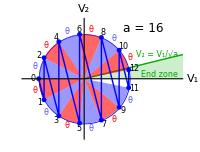

```mathematica
fig=Show[Plot[x/√a,{x,0,3},Filling->Bottom,PlotStyle->{Darker[Green],Thickness[0.005]}],
Graphics[{labels,{Blue,Thickness[0.003],Circle[{0,0},1]},fans,fans2,
anglelabels,anglelabels2,
Text[Style["End zone",Darker[Green],8],{1.65,0.1}],
Text[Style["a = 16",Italic,12],{1.3,1.12}],
Rotate[Text[Style["V_2 = V_1/√a",Darker[Green],Italic,8],{1.6,0.55}],ArcTan[1/√a]]}],
ListLinePlot[points,PlotMarkers->{Automatic,5},PlotStyle->{Blue,Thickness[0.005]}],
Axes->True,
AspectRatio->2.6/3.4, PlotRange->{{-1.3,2.1}, {-1.3,1.3}},
PlotRangePadding->None,Ticks->None,
AxesStyle->Directive[Black,Thickness[0.003],8],
AxesLabel->{"V_1","V_2"},Background->White,
ImageSize->200]
```

```mathematica
Export["3b1b_collision-sol.svg",fig]
```

3b1b_collision-sol.svg

```mathematica
Table[N[ArcTan[(2*10^d)/(10^(2d)-1)],15],{d,1,5}]
```

{0.199337304982324,0.0199993333733305,0.00199999933333373,0.000199999999333333,0.0000199999999993333}